## Flag Survey

### Raw Data

```mathematica
loc15={{1, 20}, {2,11},{3,3},{4,2},{5,1},{6,2}};
locLounge={{1,21},{2,18},{3,2},{4,0},{5,0},{6,0}};
```

### Data Processing

```mathematica
enumerateData[tab_]:=Flatten[Table[ConstantArray[tab[[i]][[1]],tab[[i]][[2]]],{i,1,Length[tab]}]]
loc15Enumerated=enumerateData[loc15]
locLoungeEnumerated=enumerateData[locLounge]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,3,3,3,4,4,5,6,6}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3}

### Data Display

```mathematica
dispInfo[tab_]:=StringForm["Mean: `` with std: ``", N@Mean[tab], N@StandardDeviation[tab]]
dispInfo[loc15Enumerated]
dispInfo[locLoungeEnumerated]
```

Mean: 1.94872 with std: 1.37551

Mean: 1.53659 with std: 0.595716

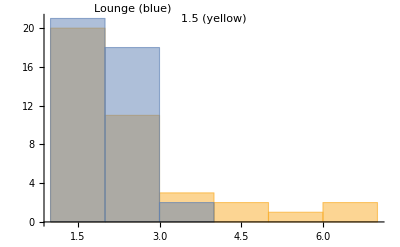

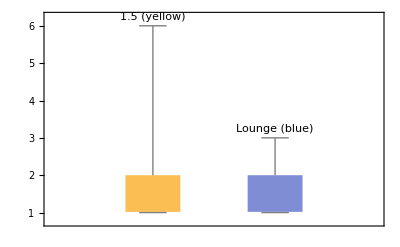

```mathematica
(*ListLinePlot[{loc15,locLounge},Filling->Axis,PlotMarkers->{Automatic, 6}]*)
Histogram[{loc15Enumerated,locLoungeEnumerated},ChartLabels->Placed[{"1.5 (yellow)","Lounge (blue)"},Above]]
BoxWhiskerChart[List[{loc15Enumerated,locLoungeEnumerated}],ChartLabels->Placed[{"1.5 (yellow)","Lounge (blue)"},Above]]
```